```mathematica
(*"Restricted" because a translational symmetry constraint is added for the first layer (see meraMap0[])), to compensate the extra freedom in "mg" layer.*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
outerProductLayer[]:=NetGraph[{ReshapeLayer[{Automatic,1}],ReshapeLayer[{1,Automatic}],DotLayer[],FlattenLayer[]},{NetPort["Input1"]->1,NetPort["Input2"]->2,{1,2}->3->4}]
reshapeLayer[dimensions_,cuts_]:=
ReshapeLayer[MovingMap[(Times@@dimensions[[#[[1]];;#[[2]]-1]])&,Join[{1},cuts,{0}],1]]
```

```mathematica
Z=1.0;
meraJoin[dimensions_]:=Module[{w0Dims=ConstantArray[dimensions[[1]],3]},
NetGraph[
<|
"input_1"->PartLayer[-1],
"input_2"->PartLayer[1],
"input_1_reshape"->reshapeLayer[dimensions,{-1}],
"input_2_reshape"->reshapeLayer[dimensions,{2}],
"w0_transpose"->TransposeLayer[1->2],
"w0_reshape"->reshapeLayer[w0Dims,{2}],
"dot_1"->DotLayer[],
"reshape"->reshapeLayer[dimensions[[;;-2]]~Join~w0Dims[[2;;]],{-1}],
"dot_2"->DotLayer[],
"w_weight"->ConstantArrayLayer["Output"->w0Dims,"Array"->RandomVariate[NormalDistribution[0,Z],w0Dims]/√(w0Dims[[-1]](**w0Dims[[-2]]*))]
|>,
{NetPort["Input"]->"input_1"->"input_1_reshape",NetPort["Input"]->"input_2"->"input_2_reshape","w_weight"->"w0_transpose"->"w0_reshape",{"input_1_reshape","w0_reshape"}->"dot_1"->"reshape",{"reshape","input_2_reshape"}->"dot_2"}]
]

meraUWW[dimensions_]:=Module[{
cut=(Length@dimensions+1)/2+1,
rotatedDims=RotateLeft[dimensions,(Length@dimensions+1)/2],
uDims=ConstantArray[dimensions[[(Length@dimensions+1)/2-1]],2]~Join~ConstantArray[dimensions[[(Length@dimensions+1)/2]],2],
wDims=ConstantArray[dimensions[[(Length@dimensions+1)/2-1]],3]
},
NetGraph[
<|
"input_reshape_in"->reshapeLayer[dimensions,{cut-1}],
"input_transpose"->TransposeLayer[],
"input_reshape_out"->reshapeLayer[RotateRight[rotatedDims,1],{3}],
"u_reshape"->reshapeLayer[uDims,{3}],
"dot_u"->DotLayer[],
"reshape_1_in"->reshapeLayer[uDims[[;;2]]~Join~rotatedDims[[2;;-2]],{-1}],
"transpose_1"->TransposeLayer[],
"reshape_1_out"->reshapeLayer[RotateRight[uDims[[;;2]]~Join~rotatedDims[[2;;-2]],1],{3}],
"w_reshape_1"->reshapeLayer[wDims,{2}],
"w_reshape_2"->reshapeLayer[wDims,{2}],
"dot_w_1"->DotLayer[],
"transpose_2"->TransposeLayer[],
"reshape_2_out"->reshapeLayer[uDims[[2;;2]]~Join~rotatedDims[[2;;-3]]~Join~wDims[[1;;1]],{3}],
"dot_w_2"->DotLayer[],
"reshape_3_in"->reshapeLayer[wDims[[1;;1]]~Join~rotatedDims[[3;;-3]]~Join~wDims[[1;;1]],{cut-2}],
"transpose_3"->TransposeLayer[],
"w1_weight"->ConstantArrayLayer["Output"->wDims,"Array"->RandomVariate[NormalDistribution[0,Z],wDims]/√(wDims[[-1]](**wDims[[-2]]*))],
"w2_weight"->ConstantArrayLayer["Output"->wDims,"Array"->RandomVariate[NormalDistribution[0,Z],wDims]/√(wDims[[-1]](**wDims[[-2]]*))],
"u_weight"-> ConstantArrayLayer["Output"->uDims,"Array"->RandomVariate[NormalDistribution[0,Z],uDims]/√(uDims[[-1]](**uDims[[-2]]*))]
|>,
{
"input_reshape_in"->"input_transpose"->"input_reshape_out",
{"u_reshape","input_reshape_out"}->"dot_u"->"reshape_1_in"->"transpose_1"->"reshape_1_out",
{"w_reshape_1","reshape_1_out"}->"dot_w_1"->"transpose_2"->"reshape_2_out",
{"w_reshape_2","reshape_2_out"}->"dot_w_2"->"reshape_3_in"->"transpose_3",
"u_weight"->"u_reshape",
"w1_weight"->"w_reshape_1",
"w2_weight"->"w_reshape_2"
}]
]

meraU[dimensions_,meraNumber_]:=Module[{
cut=(Length@dimensions+1)/2+1,
rotatedDims=RotateLeft[dimensions,(Length@dimensions+1)/2],
uDims=ConstantArray[meraNumber,2]~Join~ConstantArray[dimensions[[(Length@dimensions+1)/2]],2]
},
NetGraph[
<|
"input_reshape_in"->reshapeLayer[dimensions,{cut-1}],
"input_transpose"->TransposeLayer[],
"input_reshape_out"->reshapeLayer[RotateRight[rotatedDims,1],{3}],
"u_reshape"->reshapeLayer[uDims,{3}],
"dot_u"->DotLayer[],
"reshape_3_in"->reshapeLayer[uDims[[;;2]]~Join~rotatedDims[[2;;-2]],{cut}],
"transpose_3"->TransposeLayer[],
"u_weight"-> ConstantArrayLayer["Output"->uDims,"Array"->RandomVariate[NormalDistribution[0,Z],uDims]/√(uDims[[-1]](**uDims[[-2]]*))]
|>,
{
"input_reshape_in"->"input_transpose"->"input_reshape_out",
{"u_reshape","input_reshape_out"}->"dot_u"->"reshape_3_in"->"transpose_3",
"u_weight"->"u_reshape"
}]
]

meraW[dimensions_]:=Module[{
cut=(Length@dimensions+1)/2+1,
rotatedDims=RotateLeft[dimensions,(Length@dimensions+1)/2],
wDims=ConstantArray[dimensions[[(Length@dimensions+1)/2+1]],3]
},
NetGraph[
<|
"input_reshape_in"->reshapeLayer[dimensions,{cut-2}],
"input_transpose"->TransposeLayer[],
"input_reshape_out"->reshapeLayer[RotateRight[rotatedDims,2],{3}],
"w_reshape"->reshapeLayer[wDims,{2}],
"dot_w_1"->DotLayer[],
"reshape_3_in"->reshapeLayer[wDims[[1;;1]]~Join~rotatedDims[[;;-3]],{cut}],
"transpose_3"->TransposeLayer[],
"w_weight"-> ConstantArrayLayer["Output"->wDims,"Array"->RandomVariate[NormalDistribution[0,Z],wDims]/√(wDims[[-1]](**wDims[[-2]]*))]
|>,
{
"input_reshape_in"->"input_transpose"->"input_reshape_out",
{"w_reshape","input_reshape_out"}->"dot_w_1"->"reshape_3_in"->"transpose_3",
"w_weight"->"w_reshape"
}]
]

meraShrink[dimensions_,meraNumber_]:=Module[{
netList={},
netRules,
dims=dimensions,
order=((Length@dimensions+1)/2-1)/2-1
},
Do[
netList~AppendTo~meraUWW[dims];
dims=dims[[;;(Length@dims+1)/2-1]]~Join~dims[[(Length@dims+1)/2+2;;]],
order];
netList~AppendTo~meraU[dims,meraNumber];
netRules=Table[NetPort[i,"Output"]->NetPort[i+1,"Input"],{i,1,order}];
NetGraph[netList,netRules]
]

meraMap[dimensions_,meraNumber_,renormLags_]:=Module[{
order=(Length@dimensions+1)/2-1,
newDims=dimensions[[;;(Length@dimensions+1)/2]]~Join~{meraNumber,meraNumber}~Join~dimensions[[(Length@dimensions+1)/2+1;;]],
netList,netRules
},
netList=Table[
NetGraph[{
PartLayer[2i-1;;2i],
meraJoin[dimensions],
meraShrink[dimensions~Join~dimensions[[2;;]],meraNumber],
FlattenLayer[]
},{1->NetPort[2,"Input"],NetPort[2,"Output"]->NetPort[3,"Input"],NetPort[3,"Output"]->4}],
{i,1,renormLags/2}
]~Join~{CatenateLayer[],reshapeLayer[{renormLags/2}~Join~newDims,{2}]};
If[renormLags/2>1,
netRules={NetPort["Input"]->Table[NetPort[i,"Input"],{i,renormLags/2}],Table[NetPort[i,"Output"],{i,renormLags/2}]->renormLags/2+1->renormLags/2+2};,
netList=Delete[netList,-2];netRules={NetPort["Input"]->NetPort[1,"Input"],NetPort[1,"Output"]->renormLags/2+1}
];
NetGraph[netList,netRules]
]

meraMap0[dimension_,meraNumber_,lags_]:=Module[{netList,netRules},
netList=Table[
NetGraph[{
PartLayer[4i-3],PartLayer[4i-2],PartLayer[4i-1],PartLayer[4i],
NetChain[{TransposeLayer[3->2],TransposeLayer[2->1],ReshapeLayer[{dimension,meraNumber*meraNumber*dimension}]}],
DotLayer[],DotLayer[],
ReshapeLayer[{meraNumber*meraNumber,dimension}],ReshapeLayer[{meraNumber*meraNumber,dimension}],
DotLayer[],DotLayer[],
ReshapeLayer[{meraNumber,meraNumber}],ReshapeLayer[{meraNumber,meraNumber}],
NetChain[{TransposeLayer[1->2],ReshapeLayer[{meraNumber,meraNumber*meraNumber}]}],
DotLayer[],
ReshapeLayer[{meraNumber*meraNumber,meraNumber}],
DotLayer[],
FlattenLayer[],

ConstantArrayLayer[{meraNumber,meraNumber,dimension,dimension},"Array"->RandomVariate[NormalDistribution[0,Z],{meraNumber,meraNumber,dimension,dimension}]/√dimension]~NetInsertSharedArrays~"u",
ConstantArrayLayer[{meraNumber,meraNumber,meraNumber},"Array"->RandomVariate[NormalDistribution[0,Z],{meraNumber,meraNumber,meraNumber}]/√meraNumber]
},{
19->5,
{4,5}->6->8,{2,5}->7->9,
{8,3}->10->12,{9,1}->11->13,
20->14,
{12,14}->15->16,
{16,13}->17->18
}],
{i,1,lags/4}]~Join~{CatenateLayer[],ReshapeLayer[{lags/4,meraNumber*meraNumber*meraNumber}]};
If[lags/4>1,
netRules={NetPort["Input"]->Table[NetPort[i,"Input"],{i,lags/4}],Table[NetPort[i,"Output"],{i,lags/4}]->lags/4+1->lags/4+2},
netList=Delete[netList,-2];netRules={NetPort["Input"]->NetPort[1,"Input"],NetPort[1,"Output"]->lags/4+1}
];
NetGraph[netList,netRules]
]

meraFinish[dimensions_,hiddenVecDim_]:=Module[{
netList={},
netRules,
dims={1}~Join~dimensions[[(Length@dimensions+1)/2+1;;]]~Join~dimensions[[2;;(Length@dimensions+1)/2]],
cut=(Length@dimensions+1)/2+1,
order=(Length@dimensions+1)/2-2
},
netList~AppendTo~NetGraph[{reshapeLayer[dimensions,{cut}],TransposeLayer[],meraW[RotateLeft[dimensions,cut-1]]},{1->2->NetPort[3,"Input"]}];
Do[
netList~AppendTo~meraUWW[dims];
dims=dims[[;;(Length@dims+1)/2-1]]~Join~dims[[(Length@dims+1)/2+2;;]];,
order];
netList~AppendTo~NetChain[{LinearLayer[hiddenVecDim(*,"Biases"->None*)],ElementwiseLayer[(*LogisticSigmoid[#+2.0]&*)Tanh]}];
netList=netList~Join~Table[NetChain[{NormalizationLayer[2;;All,"Same"],ElementwiseLayer[0.5^(i-1)#&]}],{i,1,order+1}];
netRules=Table[NetPort[i,"Output"]->(order+2+i)->NetPort[i+1,"Input"],{i,1,order+1}];

NetGraph[netList,netRules]
]

mera[inputSteps_,inputVecDim_,meraNumbers_,hiddenVecDim_]:=Module[{
netList={meraMap0[inputVecDim,meraNumbers[[1]],inputSteps]},netRules,order=Length@meraNumbers-1,dims=ConstantArray[meraNumbers[[1]],3],g,a=meraNumbers~Prepend~inputVecDim
},
Do[
netList~AppendTo~meraMap[dims,meraNumbers[[i+1]],inputSteps/2^(i+1)];
dims=dims[[;;i+1]]~Join~{meraNumbers[[i+1]],meraNumbers[[i+1]]}~Join~dims[[-i;;]];
,
{i,order}];
netList~AppendTo~meraFinish[dims,hiddenVecDim];
netList=netList~Join~ConstantArray[NormalizationLayer[2;;All,"Same"],order+1];
netRules=Table[NetPort[i,"Output"]->(order+2+i)->{NetPort[i+1,"Input"],NetPort["Check"<>ToString[i]]},{i,order+1}];

g=NetGraph[netList,netRules];

NetGraph[{g,CatenateLayer[],PartLayer[-hiddenVecDim;;-1]}~Join~ConstantArray[FlattenLayer[],order+2],Table[NetPort[1,"Check"<>ToString[i]]->i+3,{i,order+1}]~Join~{NetPort[1,"Output"]->(order+5),(Range[order+2]+3)->2->3}]
]
```

```mathematica
gateLayer[n_]:=NetGraph[<|
"Wx"->LinearLayer[n,"Biases"->None],
"Ws+b"->LinearLayer[n],
"Wx+Ws+b"->TotalLayer["Inputs"->{{n},{n}}],
"e"->ElementwiseLayer[LogisticSigmoid]
|>,{NetPort["Input"]->"Wx",NetPort["State"]->"Ws+b",{"Wx","Ws+b"}->"Wx+Ws+b"->"e"}]
gateHLayer[n_]:=NetGraph[<|
"Wx"->LinearLayer[n,"Biases"->None],
"Ws+b"->LinearLayer[n],
"Wx+Ws+b"->TotalLayer["Inputs"->{{n},{n}}],
"e"->ElementwiseLayer[Tanh]
|>,{NetPort["Input"]->"Wx",NetPort["State"]->"Ws+b",{"Wx","Ws+b"}->"Wx+Ws+b"->"e"}]
gateBLayer[n_]:=NetGraph[<|
"Wx"->LinearLayer[n,"Biases"->None],
"Ws"->LinearLayer[n,"Biases"->None],
"Wx+Ws"->TotalLayer["Inputs"->{{n},{n}}],
"e"->ElementwiseLayer[LogisticSigmoid]
|>,{NetPort["Input"]->"Wx",NetPort["State"]->"Ws",{"Wx","Ws"}->"Wx+Ws"->"e"}]
gate0Layer[n_]:=NetGraph[<|
"Wx"->LinearLayer[n,"Biases"->None],
"Ws"->LinearLayer[n,"Biases"->None],
"Wx+Ws"->TotalLayer["Inputs"->{{n},{n}}]
|>,{NetPort["Input"]->"Wx",NetPort["State"]->"Ws",{"Wx","Ws"}->"Wx+Ws"}]
tensorizeLayer[k_,n_]:=NetGraph[Table[PartLayer[i],{i,k}]~Join~ConstantArray[outerProductLayer[],k-1],{NetPort["Input"]->Range[k],{1,2}->k+1,2*k-1->NetPort["OutPut"]}~Join~Table[{k-2+i,i}->k-1+i,{i,3,k}],"Input"->{k,n}]
multiGatesLayer[k_,n_]:=NetGraph[ConstantArray[gateBLayer[n-1],k]~Join~{CatenateLayer[],ReshapeLayer[{k,n-1}],PaddingLayer[{{0,0},{1,0}},"Padding"->1,"Input"->{k,n-1}]},{NetPort["Input"]->Range[k],Range[k]->k+1->k+2->k+3}]
```

```mathematica
mpsJoin[physicalDOF_,meraNumber_]:=NetGraph[{outerProductLayer[],LinearLayer[meraNumber,"Input"->physicalDOF*meraNumber,"Biases"->None,"Weights"->RandomVariate[NormalDistribution[0,Z],{meraNumber,meraNumber*physicalDOF}]/√meraNumber]},{{NetPort["Input_1"],NetPort["Input_2"]}->1->2}]

mpsLayer[k_,n_,d_]:=NetGraph[Table[PartLayer[i],{i,k}]~Join~{LinearLayer[d,"Biases"->None]}~Join~ConstantArray[mpsJoin[n,d],k-1],{NetPort["Input"]->Range[k],1->k+1,2*k->NetPort["OutPut"]}~Join~Table[{k-1+i,i}->k+i,{i,2,k}],"Input"->{k,n}]
```

```mathematica
(*Preparation of training and testing data.*)
```

```mathematica
(*Different parameters are used for different tasks.*)
```

```mathematica
(*logistic_lstm-mera.*)
meraNumbers={4,4};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=2;
inputSteps=1;
hiddenVecDim=2;

maxTrainingRounds=2*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=1;
rawData=Transpose[{NestList[4#(1-#)&,0.61,10000]}];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
rawData=Transpose[{NestList[4#(1-#)&,0.11,500]}];
testData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
```

```mathematica
(*logistic-squared_lstm-mera.*)
meraNumbers={4,4};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=2;
inputSteps=1;
hiddenVecDim=2;

maxTrainingRounds=10*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=1;
rawData=Transpose[{NestList[16#-80#^2+128#^3-64#^4&,0.61,10000]}];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
rawData=Transpose[{NestList[16#-80#^2+128#^3-64#^4&,0.11,500]}];
testData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
```

```mathematica
(*logistic-cubed_lstm-mera.*)
meraNumbers={4,4};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=2;
inputSteps=1;
hiddenVecDim=2;

maxTrainingRounds=10*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=1;
rawData=Transpose[{NestList[Function[x,64 x-1344 x^2+10752 x^3-42240 x^4+90112 x^5-106496 x^6+65536 x^7-16384 x^8],0.61,10000]}];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
rawData=Transpose[{NestList[Function[x,64 x-1344 x^2+10752 x^3-42240 x^4+90112 x^5-106496 x^6+65536 x^7-16384 x^8],0.11,500]}];
testData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
```

```mathematica
(*gauss-ar_lstm-mera.*)
meraNumbers={4};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=4;
inputSteps=16;
hiddenVecDim=4;

maxTrainingRounds=3*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=1;
rawData=NestList[{#[[2]],#[[3]],#[[4]],#[[5]],Exp[-6.2*5(-0.5#[[5]]+0.25#[[4]]-0.125#[[3]]+0.0625#[[2]]-0.03125#[[1]])^2]-0.55}&,{0.01,0.02,0.03,0.04,0.05},2*2000][[;;,-1;;-1]];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
testData=trainingData[[2001;;]];
trainingData=trainingData[[;;2000]];
```

```mathematica
(*gauss-squared_lstm-mera.*)
meraNumbers={2,2,2};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=2;
inputSteps=2;
hiddenVecDim=2;

maxTrainingRounds=10*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=1;
rawData=Transpose[{NestList[Exp[-6.2(Exp[-6.2#^2]-0.55)^2]-0.55&,0.31,10000]}];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
rawData=Transpose[{NestList[Exp[-6.2(Exp[-6.2#^2]-0.55)^2]-0.55&,0.91,500]}];
testData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
```

```mathematica
(*gauss-cubed_lstm-mera.*)
meraNumbers={2};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=2;
(*inputSteps=1;*)inputSteps=8;
hiddenVecDim=2;

maxTrainingRounds=10*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=1;
rawData=Transpose[{NestList[Exp[-6.2(Exp[-6.2(Exp[-6.2#^2]-0.55)^2]-0.55)^2]-0.55&,0.31,10000]}];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
rawData=Transpose[{NestList[Exp[-6.2(Exp[-6.2(Exp[-6.2#^2]-0.55)^2]-0.55)^2]-0.55&,0.91,500]}];
testData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
```

```mathematica
(*gauss-power5_lstm-mera.*)
meraNumbers={2,2};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=2;
inputSteps=16;
hiddenVecDim=4;

maxTrainingRounds=5*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=1;
rawData=Transpose[{NestList[Exp[-6.2(Exp[-6.2(Exp[-6.2(Exp[-6.2(Exp[-6.2#^2]-0.55)^2]-0.55)^2]-0.55)^2]-0.55)^2]-0.55&,0.31,2000]}];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
rawData=Transpose[{NestList[Exp[-6.2(Exp[-6.2(Exp[-6.2(Exp[-6.2(Exp[-6.2#^2]-0.55)^2]-0.55)^2]-0.55)^2]-0.55)^2]-0.55&,0.91,500]}];
testData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
```

```mathematica
(*Chirikov standard map.*)
meraNumbers={4,4};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=8;
inputSteps=2;
hiddenVecDim=2;

maxTrainingRounds=5*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=2;
rawData=NestList[Mod[{#[[1]]+2.0 Sin[#[[2]]],#[[2]]+#[[1]]+2.0 Sin[#[[2]]]},2π]&,{0.777,0.555},10000];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
rawData=NestList[Mod[{#[[1]]+2.0 Sin[#[[2]]],#[[2]]+#[[1]]+2.0 Sin[#[[2]]]},2π]&,{0.333,0.999},500];
testData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
```

```mathematica
(*Arnold's cat map.*)
meraNumbers={2};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=2;
inputSteps=2;
hiddenVecDim=64;

maxTrainingRounds=5*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=2;
rawData=NestList[Mod[{{2,1},{1,1}}.#,1]&,{0.777,0.555},10000];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
rawData=NestList[Mod[{{2,1},{1,1}}.#,1]&,{0.333,0.999},500];
testData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
```

```mathematica
(*Henon map (every two steps).*)
meraNumbers={2,4};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=2;
inputSteps=8;
hiddenVecDim=4;

maxTrainingRounds=5*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=1;
rawData=NestList[{#[[2]],1-1.4*#[[2]]^2+0.3*#[[1]]}&,{0.2,0.3},2*5000][[;;;;2,-1;;-1]];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
rawData=NestList[{#[[2]],1-1.4*#[[2]]^2+0.3*#[[1]]}&,{0.5,0.6},2*5000][[;;;;2,-1;;-1]];
testData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
```

```mathematica
(*lorenz-0.5_lstm-mera.*)
meraNumbers={2,3};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=2;
inputSteps=8;
hiddenVecDim=7;

maxTrainingRounds=6*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=3;
tmp=NDSolve[{x'[t]==-10.0 (x[t]-y[t]),y'[t]==-x[t] z[t]+28.0 x[t]-y[t],z'[t]==x[t] y[t]-(8/3)z[t],x[0]==z[0]==0,y[0]==1},{x,y,z},{t,0,10000},MaxSteps->∞];
rawData=Transpose[Standardize/@Transpose[Table[Flatten[{x[t],y[t],z[t]}/.tmp],{t,1,2500,0.5}]]];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
testData=trainingData[[3001;;]];
trainingData=trainingData[[;;3000]];
ListPlot[rawData[[;;1000,1]]];
```

```mathematica
(*rossler-0.5_lstm-mera.*)
meraNumbers={2,2,4};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=2;
inputSteps=4;
hiddenVecDim=4;

maxTrainingRounds=10*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=3;
tmp=NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+0.1y[t],z'[t]==0.1+z[t](x[t]-14),x[0]==z[0]==0,y[0]==1},{x,y,z},{t,0,10000},MaxSteps->∞];
rawData=Transpose[Standardize/@Transpose[Table[Flatten[{x[t],y[t],z[t]}/.tmp],{t,1,2500,0.5}]]];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
testData=trainingData[[3001;;]];
trainingData=trainingData[[;;3000]];
ListPlot[rawData[[;;1000,1]]];
```

```mathematica
(*rossler-1.0_lstm-mera.*)
meraNumbers={2,2,4};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=2;
inputSteps=4;
hiddenVecDim=4;

maxTrainingRounds=10*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=3;
tmp=NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+0.1y[t],z'[t]==0.1+z[t](x[t]-14),x[0]==z[0]==0,y[0]==1},{x,y,z},{t,0,10000},MaxSteps->∞];
rawData=Transpose[Standardize/@Transpose[Table[Flatten[{x[t],y[t],z[t]}/.tmp],{t,1,5000,1.0}]]];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
testData=trainingData[[3001;;]];
trainingData=trainingData[[;;3000]];
ListPlot[rawData[[;;1000,1]]];
```

```mathematica
(*rossler-2.0_lstm-mera.*)
meraNumbers={2,2,4};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=2;
inputSteps=4;
hiddenVecDim=4;

maxTrainingRounds=10*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=3;
tmp=NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+0.1y[t],z'[t]==0.1+z[t](x[t]-14),x[0]==z[0]==0,y[0]==1},{x,y,z},{t,0,10000},MaxSteps->∞];
rawData=Transpose[Standardize/@Transpose[Table[Flatten[{x[t],y[t],z[t]}/.tmp],{t,1,2*5000,2*1.0}]]];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
testData=trainingData[[3001;;]];
trainingData=trainingData[[;;3000]];
ListPlot[rawData[[;;1000,1]]];
```

```mathematica
(*rossler-5.0_lstm-mera.*)
meraNumbers={2,2,4};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=2;
inputSteps=4;
hiddenVecDim=4;

maxTrainingRounds=10*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=3;
tmp=NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+0.1y[t],z'[t]==0.1+z[t](x[t]-14),x[0]==z[0]==0,y[0]==1},{x,y,z},{t,0,100000},MaxSteps->∞];
rawData=Transpose[Standardize/@Transpose[Table[Flatten[{x[t],y[t],z[t]}/.tmp],{t,1,5*5000,5*1.0}]]];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
testData=trainingData[[3001;;]];
trainingData=trainingData[[;;3000]];
ListPlot[rawData[[;;1000,1]]];
```

```mathematica
(*rossler-10.0_lstm-mera.*)
meraNumbers={2,2,4};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=2;
inputSteps=4;
hiddenVecDim=4;

maxTrainingRounds=10*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=3;
tmp=NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+0.1y[t],z'[t]==0.1+z[t](x[t]-14),x[0]==z[0]==0,y[0]==1},{x,y,z},{t,0,100000},MaxSteps->∞];
rawData=Transpose[Standardize/@Transpose[Table[Flatten[{x[t],y[t],z[t]}/.tmp],{t,1,10*5000,10*1.0}]]];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
testData=trainingData[[3001;;]];
trainingData=trainingData[[;;3000]];
ListPlot[rawData[[;;1000,1]]];
```

```mathematica
(*rossler-20.0_lstm-mera.*)
meraNumbers={2,2,4};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=2;
inputSteps=4;
hiddenVecDim=4;

maxTrainingRounds=10*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=3;
tmp=NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+0.1y[t],z'[t]==0.1+z[t](x[t]-14),x[0]==z[0]==0,y[0]==1},{x,y,z},{t,0,100000},MaxSteps->∞];
rawData=Transpose[Standardize/@Transpose[Table[Flatten[{x[t],y[t],z[t]}/.tmp],{t,1,20*5000,20*1.0}]]];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
testData=trainingData[[3001;;]];
trainingData=trainingData[[;;3000]];
ListPlot[rawData[[;;1000,1]]];
```

```mathematica
(*duffing-10.0_lstm-mera.*)
meraNumbers={3,3,3,3};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=4;
inputSteps=8;
hiddenVecDim=4;

maxTrainingRounds=2*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=2;
tmp=NDSolve[{x'[t]==y[t],y'[t]==-0.02 y[t]-1.0 x[t]-5.0 x[t]^3+8.0Cos[0.5 t],x[0]==0,y[0]==1},{x,y},{t,0,100000},MaxSteps->∞];
rawData=Transpose[Standardize/@Transpose[Table[Flatten[{x[t],y[t]}/.tmp],{t,1,10*5000,10*1.0}]]];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
testData=trainingData[[3001;;]];
trainingData=trainingData[[;;3000]];
ListPlot[rawData[[;;1000,1]]];
```

```mathematica
(*thomas-1.0_lstm-mera.*)
meraNumbers={2,2,4};(*Numbers cannot be 1 because of the existence of NormalizationLayer.*)
physicalLength=2^(Length[meraNumbers]+1);
physicalDOF=4;
inputSteps=8;
hiddenVecDim=4;

maxTrainingRounds=2*20;
batchSize=64;
learningRate=0.01;
validationSet=0.2;
```

```mathematica
inputVecDim=3;
tmp=NDSolve[{x'[t]==Sin[y[t]]-0.1x[t],y'[t]==Sin[z[t]]-0.1y[t],z'[t]==Sin[x[t]]-0.1z[t],x[0]==z[0]==0,y[0]==1},{x,y,z},{t,0,50000},MaxSteps->∞];
rawData=Transpose[Standardize/@Transpose[Table[Flatten[{x[t],y[t],z[t]}/.tmp],{t,1,1*5000,1*1.0}]]];
trainingData=RandomSample[(#[[;;-2]]->#[[-1]])&/@Partition[rawData,inputSteps+1,1]];
testData=trainingData[[3001;;]];
trainingData=trainingData[[;;3000]];
ListPlot[rawData[[;;10,1]],Joined->True];
```

```mathematica
(*Training.*)
```

```mathematica
(*Basic LSTM.*)
longShortTermMemoryUnitLayer[hiddenVecDim_]:=NetGraph[<|
"i"->gateLayer[hiddenVecDim],
"o"->gateLayer[hiddenVecDim],
"f"->gateLayer[hiddenVecDim],
"m"->gateHLayer[hiddenVecDim],
"fc"->ThreadingLayer[Times],
"im"->ThreadingLayer[Times],
"fc+im"->TotalLayer["Inputs"->{{hiddenVecDim},{hiddenVecDim}}],
"e"->ElementwiseLayer[Tanh],
"oc"->ThreadingLayer[Times]
|>,{
NetPort["Input"]->NetPort["i","Input"],
NetPort["Input"]->NetPort["o","Input"],
NetPort["Input"]->NetPort["f","Input"],
NetPort["Input"]->NetPort["m","Input"],
NetPort["Input_s"]->NetPort["i","State"],
NetPort["Input_s"]->NetPort["o","State"],
NetPort["Input_s"]->NetPort["f","State"],
NetPort["Input_s"]->NetPort["m","State"],
{"f",NetPort["Input_c"]}->"fc",
{"i","m"}->"im",
{"fc","im"}->"fc+im"->NetPort["CellState"],
"fc+im"->"e",
{"o","e"}->"oc"->NetPort["State"]
}]

longShortTermMemoryLayer[hiddenVecDim_]:=NetFoldOperator[longShortTermMemoryUnitLayer[hiddenVecDim],{"CellState"->"Input_c","State"->"Input_s"}]
```

```mathematica
(*Same complexity re-settings:*)
(*(*lorenz:*)hiddenVecDim=11;*)
(*(*logistic:*)hiddenVecDim=16;*)

(*Different hyperparameter re-settings:*)
(*learningRate=0.0001;*)
(*batchSize=4;*)
```

```mathematica
rnn0=NetInitialize@NetGraph[{longShortTermMemoryLayer[hiddenVecDim],ThreadingLayer[(#1+0#2)&,"Inputs"->2],SequenceLastLayer["Input"->{Automatic,hiddenVecDim}],LinearLayer[{inputVecDim}]},{NetPort["Input"]->NetPort[1,"Input"],NetPort[1,"State"]->NetPort[2,1],NetPort[1,"CellState"]->NetPort[2,2],2->3->4},"Input"->{Automatic,inputVecDim}];
```

```mathematica
netTrainResultsObjectBenchmark0=NetTrain[rnn0,trainingData,All,ValidationSet->Scaled[validationSet],BatchSize->batchSize,(*TargetDevice->{"GPU", All},*)Method->{"ADAM","LearningRate"->learningRate(*,"L2Regularization"->10^-5*)(*,"GradientClipping"->.01*)},MaxTrainingRounds->maxTrainingRounds(*Quantity[5,"Minutes"]*)];
```

```mathematica
rnn0=netTrainResultsObjectBenchmark0["TrainedNet"];
```

```mathematica
(*LSTM-tensor.*)
longShortTermMemoryTensorUnitLayer[physicalLength_,hiddenVecDim_,physicalDOF_]:=NetGraph[<|
"i"->gateLayer[hiddenVecDim],
"o"->gateLayer[hiddenVecDim],
"f"->gateLayer[hiddenVecDim],
"m"->gateHLayer[hiddenVecDim],
"fc"->ThreadingLayer[Times],
"im"->ThreadingLayer[Times],
"fc+im"->TotalLayer["Inputs"->{{hiddenVecDim},{hiddenVecDim}}],
"e"->ElementwiseLayer[Tanh],
"oc"->ThreadingLayer[Times],
"mg"->NetChain[{LinearLayer[{physicalLength,physicalDOF-1}],NormalizationLayer[1;;All,"Same"],ElementwiseLayer[(0.2)#&],PaddingLayer[{{0,0},{1,0}},"Padding"->1,"Input"->{physicalLength,physicalDOF-1}]}],
"tensor"->NetChain[{tensorizeLayer[physicalLength,physicalDOF],LinearLayer[hiddenVecDim],ElementwiseLayer[Tanh]}]
|>,{
NetPort["Input"]->NetPort["i","Input"],
NetPort["Input"]->NetPort["o","Input"],
NetPort["Input"]->NetPort["f","Input"],
NetPort["Input"]->NetPort["m","Input"],
NetPort["Input_s"]->NetPort["i","State"],
NetPort["Input_s"]->NetPort["o","State"],
NetPort["Input_s"]->NetPort["f","State"],
NetPort["Input_s"]->NetPort["m","State"],
{"f",NetPort["Input_c"]}->"fc",
{"i","m"}->"im",
{"fc","im"}->"fc+im"->NetPort["CellState"],
"fc+im"->"e"->"mg"->"tensor",
{"o","tensor"}->"oc"->NetPort["State"]
}]
```

```mathematica
longShortTermMemoryTensorLayer[physicalLength_,hiddenVecDim_,physicalDOF_]:=NetFoldOperator[longShortTermMemoryTensorUnitLayer[physicalLength,hiddenVecDim,physicalDOF],{"CellState"->"Input_c","State"->"Input_s"}]
```

```mathematica
(*Same complexity re-settings:*)
(*(*lorenz:*)hiddenVecDim=5;physicalDOF=2;physicalLength=6;*)
(*(*logistic:*)hiddenVecDim=4;physicalDOF=2;physicalLength=8;*)
```

```mathematica
rnn1=NetInitialize@NetGraph[{longShortTermMemoryTensorLayer[physicalLength,hiddenVecDim,physicalDOF],ThreadingLayer[(#1+0#2)&,"Inputs"->2],SequenceLastLayer["Input"->{inputSteps,hiddenVecDim}],LinearLayer[{inputVecDim}]},{NetPort["Input"]->NetPort[1,"Input"],NetPort[1,"State"]->NetPort[2,1],NetPort[1,"CellState"]->NetPort[2,2],2->3->4},"Input"->{inputSteps,inputVecDim}];
```

```mathematica
netTrainResultsObjectBenchmark1=NetTrain[rnn1,RandomSample@trainingData,All,ValidationSet->Scaled[validationSet],TargetDevice->{"GPU",All},BatchSize->batchSize,Method->{"ADAM","LearningRate"->learningRate(*,"L2Regularization"->10^-5*)(*,"GradientClipping"->0.1*)},MaxTrainingRounds->maxTrainingRounds,TimeGoal->Quantity[24*60,"Minutes"]
];
```

```mathematica
rnn1=netTrainResultsObjectBenchmark1["TrainedNet"];
```

```mathematica
(*LSTM-MPS.*)
longShortTermMemoryMpsUnitLayer[physicalLength_,hiddenVecDim_,physicalDOF_,meraNumber_]:=NetGraph[<|
"i"->gateLayer[hiddenVecDim],
"o"->gateLayer[hiddenVecDim],
"f"->gateLayer[hiddenVecDim],
"m"->gateHLayer[hiddenVecDim],
"fc"->ThreadingLayer[Times],
"im"->ThreadingLayer[Times],
"fc+im"->TotalLayer["Inputs"->{{hiddenVecDim},{hiddenVecDim}}],
"e"->ElementwiseLayer[Tanh],
"oc"->ThreadingLayer[Times],
"mg"->NetChain[{LinearLayer[{physicalLength,physicalDOF-1}],NormalizationLayer[1;;All,"Same"],ElementwiseLayer[(0.2)#&],PaddingLayer[{{0,0},{1,0}},"Padding"->1,"Input"->{physicalLength,physicalDOF-1}]}],
"mps"->NetChain[{mpsLayer[physicalLength,physicalDOF,meraNumber],LinearLayer[hiddenVecDim],ElementwiseLayer[Tanh]}]
|>,{
NetPort["Input"]->NetPort["i","Input"],
NetPort["Input"]->NetPort["o","Input"],
NetPort["Input"]->NetPort["f","Input"],
NetPort["Input"]->NetPort["m","Input"],
NetPort["Input_s"]->NetPort["i","State"],
NetPort["Input_s"]->NetPort["o","State"],
NetPort["Input_s"]->NetPort["f","State"],
NetPort["Input_s"]->NetPort["m","State"],
{"f",NetPort["Input_c"]}->"fc",
{"i","m"}->"im",
{"fc","im"}->"fc+im"->NetPort["CellState"],
"fc+im"->"e"->"mg"->"mps",
{"o","mps"}->"oc"->NetPort["State"]
}];
```

```mathematica
longShortTermMemoryMpsLayer[physicalLength_,hiddenVecDim_,physicalDOF_,meraNumber_]:=NetFoldOperator[longShortTermMemoryMpsUnitLayer[physicalLength,hiddenVecDim,physicalDOF,meraNumber],{"CellState"->"Input_c","State"->"Input_s"}]
```

```mathematica
(*Same complexity re-settings:*)
(*(*lorenz:*)hiddenVecDim=7;physicalDOF=2;physicalLength=8;meraNumbers={4};*)
(*(*logistic:*)hiddenVecDim=2;physicalDOF=2;physicalLength=8;meraNumbers={9};*)
```

```mathematica
rnn2=NetInitialize@NetGraph[{longShortTermMemoryMpsLayer[physicalLength,hiddenVecDim,physicalDOF,meraNumbers[[1]]],ThreadingLayer[(#1+0#2)&,"Inputs"->2],SequenceLastLayer["Input"->{inputSteps,hiddenVecDim}],LinearLayer[{inputVecDim}]},{NetPort["Input"]->NetPort[1,"Input"],NetPort[1,"State"]->NetPort[2,1],NetPort[1,"CellState"]->NetPort[2,2],2->3->4},"Input"->{inputSteps,inputVecDim}];
```

```mathematica
netTrainResultsObjectBenchmark2=NetTrain[rnn2,RandomSample@trainingData,All,ValidationSet->Scaled[validationSet],TargetDevice->{"GPU",All},BatchSize->batchSize,Method->{"ADAM","LearningRate"->learningRate(*,"L2Regularization"->10^-5*)(*,"GradientClipping"->0.1*)},MaxTrainingRounds->maxTrainingRounds,TimeGoal->Quantity[24*60,"Minutes"]
];
```

```mathematica
rnn2=netTrainResultsObjectBenchmark2["TrainedNet"];
```

```mathematica
(*LSTM-MERA.*)
longShortTermMemoryMeraUnitLayer[physicalLength_,hiddenVecDim_,physicalDOF_,meraNumbers_]:=NetGraph[<|
"i"->gateLayer[hiddenVecDim],
"o"->gateLayer[hiddenVecDim],
"f"->gateLayer[hiddenVecDim],
"m"->gateHLayer[hiddenVecDim],
"fc"->ThreadingLayer[Times],
"im"->ThreadingLayer[Times],
"fc+im"->TotalLayer["Inputs"->{{hiddenVecDim},{hiddenVecDim}}],
"e"->ElementwiseLayer[Tanh],
"oc"->ThreadingLayer[Times],
"mg"->NetChain[{LinearLayer[{physicalLength,physicalDOF-1}],NormalizationLayer[1;;All,"Same"],ElementwiseLayer[(0.2)#&],PaddingLayer[{{0,0},{1,0}},"Padding"->1,"Input"->{physicalLength,physicalDOF-1}]}],
"mera"->mera[physicalLength,physicalDOF,meraNumbers,hiddenVecDim]
|>,{
NetPort["Input"]->NetPort["i","Input"],
NetPort["Input"]->NetPort["o","Input"],
NetPort["Input"]->NetPort["f","Input"],
NetPort["Input"]->NetPort["m","Input"],
NetPort["Input_s"]->NetPort["i","State"],
NetPort["Input_s"]->NetPort["o","State"],
NetPort["Input_s"]->NetPort["f","State"],
NetPort["Input_s"]->NetPort["m","State"],
{"f",NetPort["Input_c"]}->"fc",
{"i","m"}->"im",
{"fc","im"}->"fc+im"->NetPort["CellState"],
"fc+im"->"e"->"mg"->"mera",
{"o","mera"}->"oc"->NetPort["State"]
}]
```

```mathematica
longShortTermMemoryMeraLayer[physicalLength_,hiddenVecDim_,physicalDOF_,meraNumbers_]:=NetFoldOperator[longShortTermMemoryMeraUnitLayer[physicalLength,hiddenVecDim,physicalDOF,meraNumbers],{"CellState"->"Input_c","State"->"Input_s"}]
```

```mathematica
rnn=NetInitialize@NetGraph[{longShortTermMemoryMeraLayer[physicalLength,hiddenVecDim,physicalDOF,meraNumbers],ThreadingLayer[(#1+0#2)&,"Inputs"->2],SequenceLastLayer["Input"->{Automatic,hiddenVecDim}],LinearLayer[{inputVecDim}]},{NetPort["Input"]->NetPort[1,"Input"],NetPort[1,"State"]->NetPort[2,1],NetPort[1,"CellState"]->NetPort[2,2],2->3->4},"Input"->{Automatic,inputVecDim}];
```

```mathematica
netTrainResultsObjectBenchmark=NetTrain[rnn,RandomSample@trainingData,All,ValidationSet->Scaled[validationSet],BatchSize->batchSize,(*TargetDevice->{"GPU",All},*)Method->{"ADAM","LearningRate"->learningRate(*,"L2Regularization"->10^-5*)(*,"GradientClipping"->0.1*)},MaxTrainingRounds->maxTrainingRounds,TimeGoal->Quantity[24*60,"Minutes"],
LearningRateMultipliers->Table[{1,"Net","mera",1,i}->(learningRateMultipliers=0.5),{i,Length@meraNumbers+1}]
];
```

```mathematica
rnn=netTrainResultsObjectBenchmark["TrainedNet"];
```

```mathematica
rnnGood=rnn;
```

```mathematica
(*Test and comparison.*)
```

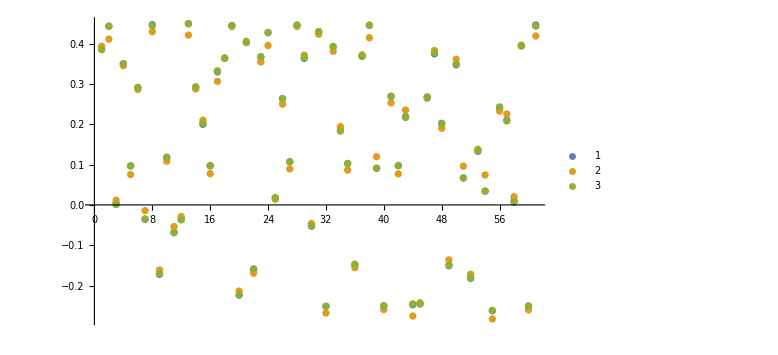

```mathematica
testDataSamples=testData[[200;;260]];
ListPlot[{
testDataSamples[[;;,2]][[;;,-1]],
(rnn0/@testDataSamples[[;;,1]])[[;;,-1]],
(rnn/@testDataSamples[[;;,1]])[[;;,-1]](*,
(rnnGood/@testDataSamples[[;;,1]])[[;;,1]],
(meraCone/@testDataSamples[[;;,1]])[[;;,1]]*)
},PlotRange->All,PlotLegends->Automatic,PlotStyle->Opacity[1],ImageSize->Large]
```

```mathematica
testDataSamples=testData[[;;]];
N@Mean[Flatten[(Function[x,Subtract[Mean[#],x]]/@#)&@testDataSamples[[;;,2]]]^2]
rnn0Err=Mean[Flatten[(rnn0Predict=ParallelMap[rnn0[#,TargetDevice->"CPU"]&,testDataSamples[[;;,1]]])-testDataSamples[[;;,2]]]^2]
rnnErr=Mean[Flatten[(rnnPredict=ParallelMap[rnn[#,TargetDevice->"CPU"]&,testDataSamples[[;;,1]]])-testDataSamples[[;;,2]]]^2]
```

0.0525972

0.000236989

3.73706×10^-6

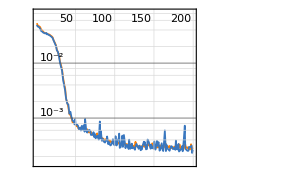
NetTrain Results
summary | ,,  batches:25000  rounds:200  time:46s  examples/s:34894
data | ,,  training examples:8000  validation examples:2048  processed examples:1600000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.75×10^-4
validation | ,,  loss:2.64×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

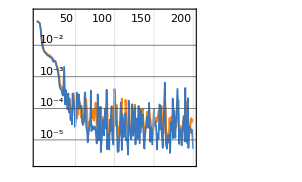
NetTrain Results
summary | ,,  batches:25000  rounds:200  time:4.4min  examples/s:6096
data | ,,  training examples:8000  validation examples:2048  processed examples:1600000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:4.1×10^-5
validation | ,,  loss:5.17×10^-6
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netTrainResultsObjectBenchmark0
netTrainResultsObjectBenchmark
```

```mathematica
DumpSave[NotebookDirectory[]<>"gauss-cubed_lstm-mera_statistical.mx","Global`"];
```

```mathematica
<<(NotebookDirectory[]<>"gauss-cubed_lstm-mera.mx")
```

```mathematica
rnn0Err
rnnErr
```

0.000236989

3.73706×10^-6

```mathematica
(*Same complexity test.*)
```

```mathematica
freeArraysElementCounts[nn_]:=Module[{
counts=Normal[NetInformation[nn,"ArraysElementCounts"]],
matches
},
matches=Select[counts[[;;,1]],(MemberQ[#,"Scaling"])&];
matches=matches~Join~Replace[matches,"Scaling"->"Biases",∞];
(*Print[matches];*)
Total[Select[counts,Not@MemberQ[matches,#[[1]]]&][[;;,2]]]
]
```

```mathematica
(*NetInformation[rnn,"ArraysTotalElementCount"]*)
freeArraysElementCounts[rnn]
(*NetInformation[rnn0,"ArraysTotalElementCount"]*)
freeArraysElementCounts[rnn0]
(*NetInformation[rnn1,"ArraysTotalElementCount"]*)
freeArraysElementCounts[rnn1]
(*NetInformation[rnn2,"ArraysTotalElementCount"]*)
freeArraysElementCounts[rnn2]
```

```mathematica
rnn0Err=Mean[(Flatten[ParallelMap[rnn0[#,TargetDevice->"CPU"]&,testDataSamples[[;;,1]]]-testDataSamples[[;;,2]]])^2]
```

0.0940125

```mathematica
rnn1Err=Mean[Flatten[ParallelMap[rnn1[#,TargetDevice->"CPU"]&,testDataSamples[[;;,1]]]-testDataSamples[[;;,2]]]^2]
```

0.00009662

```mathematica
rnn2Err=Mean[Flatten[ParallelMap[rnn2[#,TargetDevice->"CPU"]&,testDataSamples[[;;,1]]]-testDataSamples[[;;,2]]]^2]
```

0.00783064

```mathematica
(*Tests on alternative positions of the MERA layer.*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<(NotebookDirectory[]<>"thomas-1.0_lstm-mera_alternative-2.mx")
```

```mathematica
(*LSTM-mera. Alternative 6.*)
longShortTermMemoryMeraUnitLayer[physicalLength_,hiddenVecDim_,physicalDOF_,meraNumbers_]:=NetGraph[<|
"i"->gateLayer[hiddenVecDim],
"o"->gateLayer[hiddenVecDim],
"f"->gateLayer[hiddenVecDim],
"m"->gateHLayer[hiddenVecDim],
"fc"->ThreadingLayer[Times],
"im"->ThreadingLayer[Times],
"fc+im"->TotalLayer["Inputs"->{{hiddenVecDim},{hiddenVecDim}}],
"e"->ElementwiseLayer[Tanh],
"oc"->ThreadingLayer[Times],
"mg"->NetChain[{LinearLayer[{physicalLength,physicalDOF-1}],NormalizationLayer[1;;All,"Same"],ElementwiseLayer[(0.2)#&],PaddingLayer[{{0,0},{1,0}},"Padding"->1,"Input"->{physicalLength,physicalDOF-1}]}],
"mera"->mera[physicalLength,physicalDOF,meraNumbers,hiddenVecDim]
|>,{
NetPort["Input"]->NetPort["i","Input"],
NetPort["Input"]->NetPort["o","Input"],
NetPort["Input"]->NetPort["f","Input"],
NetPort["Input"]->NetPort["m","Input"],
NetPort["Input_s"]->NetPort["i","State"],
NetPort["Input_s"]->NetPort["o","State"],
NetPort["Input_s"]->NetPort["f","State"],
NetPort["Input_s"]->NetPort["m","State"],
{"f",NetPort["Input_c"]}->"fc",
{"i","m"}->"im",
{"fc","im"}->"fc+im"->"mg"->"mera"->NetPort["CellState"],
"fc+im"->"e",
{"o","e"}->"oc"->NetPort["State"]
}]
```

```mathematica
(*LSTM-mera. Alternative 7.*)
longShortTermMemoryMeraUnitLayer[physicalLength_,hiddenVecDim_,physicalDOF_,meraNumbers_]:=NetGraph[<|
"i"->gateLayer[hiddenVecDim],
"o"->gateLayer[hiddenVecDim],
"f"->gateLayer[hiddenVecDim],
"m"->gateHLayer[hiddenVecDim],
"fc"->ThreadingLayer[Times],
"im"->ThreadingLayer[Times],
"fc+im"->TotalLayer["Inputs"->{{hiddenVecDim},{hiddenVecDim}}],
"e"->ElementwiseLayer[Tanh],
"oc"->ThreadingLayer[Times],
"mg"->NetChain[{LinearLayer[{physicalLength,physicalDOF-1}],NormalizationLayer[1;;All,"Same"],ElementwiseLayer[(0.2)#&],PaddingLayer[{{0,0},{1,0}},"Padding"->1,"Input"->{physicalLength,physicalDOF-1}]}],
"mera"->mera[physicalLength,physicalDOF,meraNumbers,hiddenVecDim]
|>,{
NetPort["Input"]->NetPort["i","Input"],
NetPort["Input"]->NetPort["o","Input"],
NetPort["Input"]->NetPort["f","Input"],
NetPort["Input"]->NetPort["m","Input"],
NetPort["Input_s"]->NetPort["i","State"],
NetPort["Input_s"]->NetPort["o","State"],
NetPort["Input_s"]->NetPort["f","State"],
NetPort["Input_s"]->NetPort["m","State"],
{"f",NetPort["Input_c"]}->"fc",
{"i","m"}->"im",
{"fc","im"}->"fc+im"->NetPort["CellState"],
"fc+im"->"e",
"o"->"mg"->"mera",
{"mera","e"}->"oc"->NetPort["State"]
}]
```

```mathematica
(*LSTM-mera. Alternative 8.*)
longShortTermMemoryMeraUnitLayer[physicalLength_,hiddenVecDim_,physicalDOF_,meraNumbers_]:=NetGraph[<|
"i"->gateLayer[hiddenVecDim],
"o"->gateLayer[hiddenVecDim],
"f"->gateLayer[hiddenVecDim],
"m"->gateHLayer[hiddenVecDim],
"fc"->ThreadingLayer[Times],
"im"->ThreadingLayer[Times],
"fc+im"->TotalLayer["Inputs"->{{hiddenVecDim},{hiddenVecDim}}],
"e"->ElementwiseLayer[Tanh],
"oc"->ThreadingLayer[Times],
"mg"->NetChain[{LinearLayer[{physicalLength,physicalDOF-1}],NormalizationLayer[1;;All,"Same"],ElementwiseLayer[(0.2)#&],PaddingLayer[{{0,0},{1,0}},"Padding"->1,"Input"->{physicalLength,physicalDOF-1}]}],
"mera"->mera[physicalLength,physicalDOF,meraNumbers,hiddenVecDim]
|>,{
NetPort["Input"]->NetPort["i","Input"],
NetPort["Input"]->NetPort["o","Input"],
NetPort["Input"]->NetPort["f","Input"],
NetPort["Input"]->NetPort["m","Input"],
NetPort["Input_s"]->NetPort["i","State"],
NetPort["Input_s"]->NetPort["o","State"],
NetPort["Input_s"]->NetPort["f","State"],
NetPort["Input_s"]->NetPort["m","State"],
{"f",NetPort["Input_c"]}->"fc",
{"i","m"}->"im"->"mg"->"mera",
{"fc","mera"}->"fc+im"->NetPort["CellState"],
"fc+im"->"e",
{"o","e"}->"oc"->NetPort["State"]
}]
```

```mathematica
(*Statistical models.*)
```

```mathematica
(*ARMA*)(*gauss-cubed_lstm-mera.*)
trainingTS=NestList[Exp[-6.2(Exp[-6.2(Exp[-6.2#^2]-0.55)^2]-0.55)^2]-0.55&,0.31,10000];
armaProcess=EstimatedProcess[trainingTS,ARMAProcess[c,Table[Subscript[a,i],{i,7}],Table[Subscript[b,i],{i,7}],ν](*,"ProcessEstimator"->"MethodOfMoments"*)]
armaProcess=Normal@TimeSeriesModelFit[trainingTS]
```

ARMAProcess[0.144359,{0.419786,-0.202603,-0.0235858,-0.380169,-0.0291338,0.0300952,0.0842895},{-0.635895,0.0419101,0.234918,0.29811,-0.162529,-0.0298303,-0.0313746},0.0482717]

ARMAProcess[0.110442,{0.0171973,-0.17593,0.316166},{-0.234564,-0.0739516,-0.199683,0.0580327},0.0482888]

```mathematica
TimeSeriesForecast[armaProcess,Flatten[#],1,Method->"Kalman"]&/@testData[[;;,1]];
Mean[(%-Flatten[testData[[;;,2]]])^2]
```

0.0622258

```mathematica
gbt=Predict[trainingData[[;;,1]]->Flatten[trainingData[[;;,2]]],
TargetDevice->"CPU",Method->{"GradientBoostedTrees","LearningRate"->learningRate,MaxTrainingRounds->maxTrainingRounds,"MaxDepth"->8}
];
```

```mathematica
Mean[(gbt/@testData[[;;,1]]-Flatten[testData[[;;,2]]])^2]
```

0.000992701

```mathematica
nn=Predict[trainingData[[;;,1]]->Flatten[trainingData[[;;,2]]],
TargetDevice->"CPU",PerformanceGoal->"Quality",Method->{"NeuralNetwork",MaxTrainingRounds->maxTrainingRounds,ValidationSet->Scaled[validationSet],
"NetworkType"->"FullyConnected"
(*,
(*"NumberOfParameters"->500,"NetInitializationMethod"->"Random","OptimizationMethod"->{"ADAM","LearningRate"->learningRate},*)
"NetworkDepth"->8,
"NetTrainOptions"->{ValidationSet->Scaled[validationSet],BatchSize->batchSize,Method->{"ADAM","LearningRate"->learningRate},MaxTrainingRounds->maxTrainingRounds}*)
}
];
```

```mathematica
nn[[1,"TrainingInformation"]]
```

<|PanelCell→184721,TrainingFunction→Predict,EMIterations→Missing[KeyAbsent,EMIterations],ProcessorEntropyShift→-1.44469,PreprocessingTime→8.64263,LossName→StandardDeviation,BestModelInformation→Dataset[<>],Configurations→Dataset[<>],MaxTrainingSize→9993,PreprocessorEvaluationTime→3.128×10^-6,PreprocessorMemory→39264,InputDimension→8,OutputDimension→1,BaselineLogProbability→-1.41894,VariableBudget→True,CheckpointingInfo→<|Checkpointing→False|>,UserStop→False,NaturalStop→True,AbortStop→False,LastReportingTime→3.785692263296391×10^9,RoundPartitioning→Dataset[<>]|>

```mathematica
Mean[(nn/@testData[[;;,1]]-Flatten[testData[[;;,2]]])^2]
```

0.0000663407

```mathematica
(*"Higher-order" (HO) LSTM.*)
```

```mathematica
(*LSTM. Alternative 4.*)
longShortTermMemoryUnitLayer[physicalLength_,hiddenVecDim_]:=NetGraph[<|
"i"->gateLayer[hiddenVecDim],
"o"->gateLayer[hiddenVecDim],
"f"->gateLayer[hiddenVecDim],
"m"->gateHLayer[hiddenVecDim],
"fc"->ThreadingLayer[Times],
"im"->ThreadingLayer[Times],
"fc+im"->TotalLayer["Inputs"->{{hiddenVecDim},{hiddenVecDim}}],
"e"->ElementwiseLayer[Tanh],
"oc"->ThreadingLayer[Times],
"sr"->SequenceRestLayer[],
"c"->AppendLayer[]
|>,{
NetPort["Input"]->NetPort["i","Input"],
NetPort["Input"]->NetPort["o","Input"],
NetPort["Input"]->NetPort["f","Input"],
NetPort["Input"]->NetPort["m","Input"],
NetPort["Input_s"]->NetPort["i","State"],
NetPort["Input_s"]->NetPort["o","State"],
NetPort["Input_s"]->NetPort["f","State"],
NetPort["Input_s"]->NetPort["m","State"],
{"f",NetPort["Input_c"]}->"fc",
{"i","m"}->"im",
{"fc","im"}->"fc+im"->NetPort["CellState"],
"fc+im"->"e",
{"o","e"}->"oc"->NetPort["c","Element"],
NetPort["Input_s"]->"sr"-> NetPort["c","Input"],
"c"->NetPort["State"]
},"Input_s"->{physicalLength,hiddenVecDim}]
```

```mathematica
longShortTermMemoryLayer[physicalLength_,hiddenVecDim_]:=NetFoldOperator[longShortTermMemoryUnitLayer[physicalLength,hiddenVecDim],{"CellState"->"Input_c","State"->"Input_s"}]
```

```mathematica
rnn0=NetInitialize@NetGraph[{longShortTermMemoryLayer[physicalLength,hiddenVecDim],ThreadingLayer[(#1+0#2)&,"Inputs"->2],(*SequenceLastLayer["Input"->{Automatic,hiddenVecDim}],*)LinearLayer[{inputVecDim}],SequenceLastLayer[],SequenceLastLayer[],SequenceLastLayer[]},{NetPort["Input"]->NetPort[1,"Input"],NetPort[1,"State"]->5->6->NetPort[2,1],NetPort[1,"CellState"]->4->NetPort[2,2],2->3},"Input"->{Automatic,inputVecDim}];
```

```mathematica
netTrainResultsObjectBenchmark0=NetTrain[rnn0,RandomSample@trainingData,All,ValidationSet->Scaled[validationSet],BatchSize->batchSize,(*TargetDevice->{"GPU",All},*)Method->{"ADAM","LearningRate"->learningRate(*,"L2Regularization"->10^-5*)(*,"GradientClipping"->0.1*)},MaxTrainingRounds->maxTrainingRounds,TimeGoal->Quantity[24*60,"Minutes"](*,
LearningRateMultipliers->Table[{1,"Net","mera",1,i}->(learningRateMultipliers=0.5),{i,Length@meraNumbers+1}]*)
];
```

```mathematica
rnn0=netTrainResultsObjectBenchmark0["TrainedNet"];
```

```mathematica
(*"Higher-order MPS" (HOT) LSTM.*)
```

```mathematica
gateMpsLayer[physicalLength_,hiddenVecDim_,physicalDOF_,meraNumber_]:=NetGraph[<|
"Wx"->LinearLayer[hiddenVecDim],
"flatten"->FlattenLayer[],
"pad"->PaddingLayer[{{1,0}},"Padding"->1,"Input"->{physicalLength*hiddenVecDim}],
"rep"->ReplicateLayer[physicalDOF],
"transpose"->TransposeLayer[],
"mps"->NetChain[{mpsLayer[physicalLength*hiddenVecDim+1,physicalDOF,meraNumber],LinearLayer[hiddenVecDim](*,ElementwiseLayer[Tanh]*)}],
"Wx+mps"->TotalLayer["Inputs"->{{hiddenVecDim},{hiddenVecDim}}],
"e"->ElementwiseLayer[LogisticSigmoid[#]&]
|>,{NetPort["Input"]->"Wx",NetPort["State"]->"flatten"->"pad"->"rep"->"transpose"->"mps",{"Wx","mps"}->"Wx+mps"->"e"}]
```

```mathematica
(*LSTM-mps. Alternative 4. Remember to use LogisticSigmoid.*)
longShortTermMemoryMpsUnitLayer[physicalLength_,hiddenVecDim_,physicalDOF_,meraNumber_]:=NetGraph[<|
"i"->gateMpsLayer[physicalLength,hiddenVecDim,physicalDOF,meraNumber],
"f"->gateMpsLayer[physicalLength,hiddenVecDim,physicalDOF,meraNumber],
"o"->gateMpsLayer[physicalLength,hiddenVecDim,physicalDOF,meraNumber],
"m"->gateMpsLayer[physicalLength,hiddenVecDim,physicalDOF,meraNumber],
"fc"->ThreadingLayer[Times],
"im"->ThreadingLayer[Times],
"fc+im"->TotalLayer["Inputs"->{{hiddenVecDim},{hiddenVecDim}}],
"e"->ElementwiseLayer[Tanh],
"oc"->ThreadingLayer[Times],
"sr"->SequenceRestLayer[],
"c"->AppendLayer[]
|>,{
NetPort["Input"]->NetPort["i","Input"],
NetPort["Input"]->NetPort["o","Input"],
NetPort["Input"]->NetPort["f","Input"],
NetPort["Input"]->NetPort["m","Input"],
NetPort["Input_s"]->NetPort["i","State"],
NetPort["Input_s"]->NetPort["o","State"],
NetPort["Input_s"]->NetPort["f","State"],
NetPort["Input_s"]->NetPort["m","State"],
{"f",NetPort["Input_c"]}->"fc",
{"i","m"}->"im",
{"fc","im"}->"fc+im"->NetPort["CellState"],
"fc+im"->"e",
{"o","e"}->"oc"->NetPort["c","Element"],
NetPort["Input_s"]->"sr"-> NetPort["c","Input"],
"c"->NetPort["State"]
},"Input_s"->{physicalLength,hiddenVecDim}]
```

```mathematica
longShortTermMemoryMpsLayer[physicalLength_,hiddenVecDim_,physicalDOF_,meraNumber_]:=NetFoldOperator[longShortTermMemoryMpsUnitLayer[physicalLength,hiddenVecDim,physicalDOF,meraNumber],{"CellState"->"Input_c","State"->"Input_s"}]
```

```mathematica
rnn2=NetInitialize@NetGraph[{longShortTermMemoryMpsLayer[physicalLength,hiddenVecDim,physicalDOF,meraNumbers[[1]]],ThreadingLayer[(#1+0#2)&,"Inputs"->2],(*SequenceLastLayer["Input"->{Automatic,hiddenVecDim}],*)LinearLayer[{inputVecDim}],SequenceLastLayer[],SequenceLastLayer[],SequenceLastLayer[]},{NetPort["Input"]->NetPort[1,"Input"],NetPort[1,"State"]->5->6->NetPort[2,1],NetPort[1,"CellState"]->4->NetPort[2,2],2->3},"Input"->{Automatic,inputVecDim}];
```

```mathematica
netTrainResultsObjectBenchmark2=NetTrain[rnn2,RandomSample@trainingData,All,ValidationSet->Scaled[validationSet],(*TargetDevice->{"GPU",All},*)BatchSize->batchSize,Method->{"ADAM","LearningRate"->learningRate(*,"L2Regularization"->10^-5*)(*,"GradientClipping"->0.1*)},MaxTrainingRounds->maxTrainingRounds,TimeGoal->Quantity[24*60,"Minutes"]
];
```

```mathematica
rnn2=netTrainResultsObjectBenchmark2["TrainedNet"];
```

```mathematica
(*"Higher-order" (HO) RNN.*)
```

```mathematica
recurrentUnitLayer[physicalLength_,hiddenVecDim_]:=NetGraph[<|
"i"->gateLayer[hiddenVecDim],
"sr"->SequenceRestLayer[],
"c"->AppendLayer[]
|>,{
NetPort["Input"]->NetPort["i","Input"],
NetPort["Input_s"]->NetPort["i","State"],
"i"->NetPort["c","Element"],
NetPort["Input_s"]->"sr"-> NetPort["c","Input"],
"c"->NetPort["State"]
},"Input_s"->{physicalLength,hiddenVecDim}]
```

```mathematica
recurrentLayer[physicalLength_,hiddenVecDim_]:=NetFoldOperator[recurrentUnitLayer[physicalLength,hiddenVecDim],{"State"->"Input_s"}]
```

```mathematica
rnn00=NetInitialize@NetGraph[{recurrentLayer[physicalLength,hiddenVecDim],LinearLayer[{inputVecDim}],SequenceLastLayer[],SequenceLastLayer[]},{NetPort["Input"]->NetPort[1,"Input"],NetPort[1,"State"]->4->3->2},"Input"->{Automatic,inputVecDim}];
```

```mathematica
netTrainResultsObjectBenchmark00=NetTrain[rnn00,RandomSample@trainingData,All,ValidationSet->Scaled[validationSet],(*TargetDevice->{"GPU",All},*)BatchSize->batchSize,Method->{"ADAM","LearningRate"->learningRate(*,"L2Regularization"->10^-5*)(*,"GradientClipping"->0.1*)},MaxTrainingRounds->maxTrainingRounds,TimeGoal->Quantity[24*60,"Minutes"]
];
```

```mathematica
rnn00=netTrainResultsObjectBenchmark00["TrainedNet"];
```

```mathematica
(*"Higher-order MPS" (HOT) RNN.*)
recurrentMpsUnitLayer[physicalLength_,hiddenVecDim_,physicalDOF_,meraNumber_]:=NetGraph[<|
"i"->gateMpsLayer[physicalLength,hiddenVecDim,physicalDOF,meraNumber],
"sr"->SequenceRestLayer[],
"c"->AppendLayer[]
|>,{
NetPort["Input"]->NetPort["i","Input"],
NetPort["Input_s"]->NetPort["i","State"],
"i"->NetPort["c","Element"],
NetPort["Input_s"]->"sr"-> NetPort["c","Input"],
"c"->NetPort["State"]
},"Input_s"->{physicalLength,hiddenVecDim}]
```

```mathematica
recurrentMpsLayer[physicalLength_,hiddenVecDim_,physicalDOF_,meraNumber_]:=NetFoldOperator[recurrentMpsUnitLayer[physicalLength,hiddenVecDim,physicalDOF,meraNumber],{"State"->"Input_s"}]
```

```mathematica
rnn02=NetInitialize@NetGraph[{recurrentMpsLayer[physicalLength,hiddenVecDim,physicalDOF,meraNumbers[[1]]],LinearLayer[{inputVecDim}],SequenceLastLayer[],SequenceLastLayer[]},{NetPort["Input"]->NetPort[1,"Input"],NetPort[1,"State"]->4->3->2},"Input"->{Automatic,inputVecDim}];
```

```mathematica
netTrainResultsObjectBenchmark02=NetTrain[rnn02,RandomSample@trainingData,All,ValidationSet->Scaled[validationSet],(*TargetDevice->{"GPU",All},*)BatchSize->batchSize,Method->{"ADAM","LearningRate"->learningRate(*,"L2Regularization"->10^-5*)(*,"GradientClipping"->0.1*)},MaxTrainingRounds->maxTrainingRounds,TimeGoal->Quantity[24*60,"Minutes"]
];
```

```mathematica
rnn02=netTrainResultsObjectBenchmark02["TrainedNet"];
```

```mathematica
rnn0Err=Mean[Flatten[ParallelMap[rnn0[#,TargetDevice->"CPU"]&,testDataSamples[[;;,1]]]-testDataSamples[[;;,2]]]^2]
rnn2Err=Mean[Flatten[ParallelMap[rnn2[#,TargetDevice->"CPU"]&,testDataSamples[[;;,1]]]-testDataSamples[[;;,2]]]^2]
rnn00Err=Mean[Flatten[ParallelMap[rnn00[#,TargetDevice->"CPU"]&,testDataSamples[[;;,1]]]-testDataSamples[[;;,2]]]^2]
rnn02Err=Mean[Flatten[ParallelMap[rnn02[#,TargetDevice->"CPU"]&,testDataSamples[[;;,1]]]-testDataSamples[[;;,2]]]^2]
```

0.000874318

0.000191925

0.0141783

0.0145003